# Constrained Optimization, Derivatives and Taylor Series

We can see minima in 2D.  For now we are going to assume that there are no equality constraints.

Mathematica can compute derivatives of “calculus” like functions.  What we want is equations involving the derivatives of the scalar objective f(x) and the inequality constraint function g_i(x) that we can “solve” to find the minimum.  They have to be able to deal with multiple constraints.  The key idea is Lagrange multipliers.

## “Types” of Minima

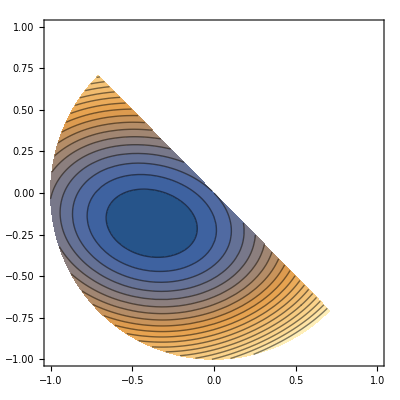

```mathematica
f[{x1_,x2_}]:= x1^2+2 x2^2+ArcTan[x1 + x2 Cos[x1-Sin[x1+x2]]]
ContourPlot[f[{x1,x2}],{x1,-1,1},{x2,-1,1},
Contours->40,
RegionFunction->Function[{x1,x2},And[1-(x1^2+x2^2)>0,-(x1+x2)>0]]
]
```

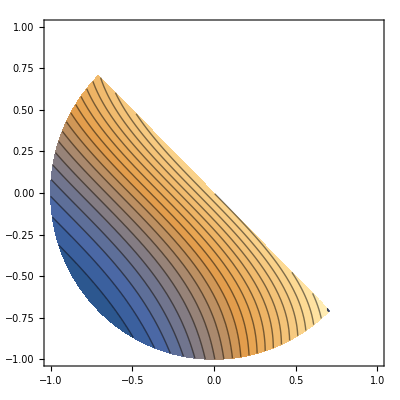

```mathematica
f[{x1_,x2_}]:= ArcTan[x1 + x2 Cos[x1-Sin[x1+x2]]]
ContourPlot[f[{x1,x2}],{x1,-1,1},{x2,-1,1},
Contours->40,
RegionFunction->Function[{x1,x2},And[1-(x1^2+x2^2)>0,-(x1+x2)>0]]
]
```

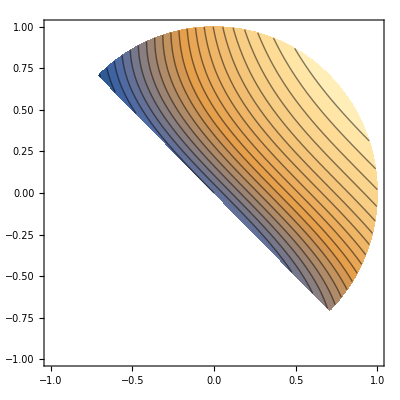

```mathematica
f[{x1_,x2_}]:= ArcTan[x1 + x2 Cos[x1-Sin[x1+x2]]]
ContourPlot[f[{x1,x2}],{x1,-1,1},{x2,-1,1},
Contours->40,
RegionFunction->Function[{x1,x2},And[1-(x1^2+x2^2)>0,(x1+x2)>0]]
]
```

## Taylor Series

Lets look at Taylor Series for the objective function f.

```mathematica
f[{x1_,x2_}]:= x1^2+2 x2^2+ArcTan[x1 + x2 Cos[x1-Sin[x1+x2]]]
p0={x10,x20}={-0.1,-0.1};
Show[
Plot3D[ f[{x1,x2}],{x1,-1,1},{x2,-1,1},RegionFunction->Function[{x1,x2},And[1-(x1^2+x2^2)>0,-(x1+x2)>0]]
],
Graphics3D[{Green, PointSize[0.02],Point[{x10,x20,f[{x10,x20}]}]}]]
```

-Graphics3D-

```mathematica
f[{x1_,x2_}]:= x1^2+2 x2^2+ArcTan[x1 + x2 Cos[x1-Sin[x1+x2]]]
p0={-0.1,-0.1};
Show[
Plot3D[ f[{x1,x2}],{x1,-1,1},{x2,-1,1},RegionFunction->Function[{x1,x2},And[1-(x1^2+x2^2)>0,-(x1+x2)>0]]
],
Graphics3D[{Green, PointSize[0.02],Point[{x10,x20,f[p0]}]}]]
```